## Paquetes y definiciones

### Fijar directorio, cargar paquetes y encender kernels

```mathematica
(* Fijar directorio a mis archivos dentro del repositorio *)
SetDirectory[NotebookDirectory[]];

(* Cargar paquetes *)
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
```

```mathematica
(* Encender los kernels *)
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Parámetros

```mathematica
L=8;(* espines *)
```

```mathematica
(* valores para (hz, J) *)
hx=1.;
{hz0,hzf,hzStep}={0.01,3.01,0.5};
{J0,Jf,Jstep}={1.,1.,0.};
hzAndJvalues=Tuples[{Range[hz0,hzf,hzStep],Range[J0,Jf,Jstep]}]
```

{{0.01,1.},{0.51,1.},{1.01,1.},{1.51,1.},{2.01,1.},{2.51,1.},{3.01,1.}}

```mathematica
(* tiempos para la curva de Haar *)
{t0,tf,tStep}={0.,50.,0.5};
```

```mathematica
(* Nombre de archivo para guardar el promedio temporal del valor esperado de Haar de la pureza de Choi *)
temporalAvgOfHaarAvgOfChoiPurityFilename="data/temporal_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[NumberForm[L,{Infinity,0}]]<>"_hx_"<>ToString[NumberForm[hx,{Infinity,2}]]<>".csv"
```

data/temporal_haar_avg_choi_purity/wisniacki_open_L_4_hx_1.00.csv

## Valor esperado de Haar de la pureza de Choi

```mathematica
pauliIndices=Tuples[Range[0,3],L-1];

(* Pauli strings with fixed σ_1 = id *)
pauliStrings=Pauli[Join[{0},#]]&/@pauliIndices;

constants=(1/2)^2*(1/12)^(L-1)*Power[3.,(L-1)-Count[#,x_/;x!=0]]&/@pauliIndices;

(* Lista de tiempos por cada iteración del Do *)
times={};

lenhzAndJvalues = Length[hzAndJvalues];

dimH=2^L;
halfDimH=dimH/2;
halfDimHPlusOne=dimH/2+1;
```

```mathematica
(* Archivo para guardar promedio temporal del valor esperado de Haar de la pureza de Choi *)
dataFile=OpenAppend[temporalAvgOfHaarAvgOfChoiPurityFilename];
WriteString[dataFile,"hz,J,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi"<>"\n"];
Close[dataFile];
```

```mathematica
Do[

(* hz y J *)
{hz,J}=hzAndJvalues[[hzAndJ]];

(* Crear Hamiltoniano y diagonalizar *)
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalues, eigenvectors}=Chop[Eigensystem[H]];

(* Calcular la matriz de cambio de base de la de eigenenergías a la computacional *)
P = Transpose[eigenvectors];

(* Operador de evolución *)
ClearAll[U];U[t_]:=U[t]=P.DiagonalMatrix[Exp[-I*eigenvalues*t]].ConjugateTranspose[P];

(* Calcular valor esperado de Haar de la pureza de Choi para cada t *)
haarAvgChoiPurity = {};
Do[
u=U[t];uDagger=ConjugateTranspose[u];
h=Total[
ParallelTable[
(* Compute partial trace *)
A=#[[1;;halfDimH,1;;halfDimH]]+#[[halfDimHPlusOne;;dimH,halfDimHPlusOne;;dimH]]&[u.pauliStrings[[i]].uDagger,L];
(* Purity *)
Chop[constants[[i]]*Tr[A.A]]
,{i,4^(L-1)}
,DistributedContexts->Full
,ProgressReporting->False]
];
AppendTo[haarAvgChoiPurity,{t,h}]
	,{t,t0,tf,tStep}];

Export["data_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>".m",haarAvgChoiPurity];

(* Calcular el promedio temporal de la pureza promedio de Choi *)
fInterp = Interpolation[haarAvgChoiPurity]; 
haarAvgChoiPurityTempAvg = NIntegrate[fInterp[t],{t,t0,tf}]/tf;
Export["meandata_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>".m",haarAvgChoiPurityTempAvg];

,{hzAndJ,lenhzAndJvalues}];
```

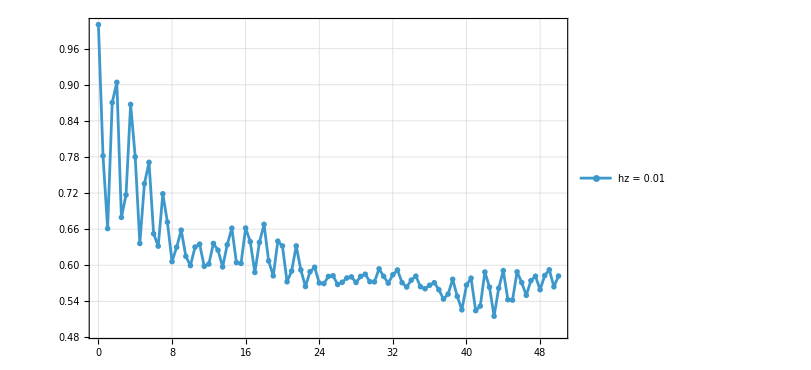

```mathematica
ListPlot[haarAvgChoiPurity,Joined->True,PlotMarkers->"OpenMarkers",PlotRange->Full,PlotLegends->("hz = "<>ToString[NumberForm[#,{Infinity,2}]]&/@hzAndJvalues[[All,1]]),PlotTheme->"Detailed",ImageSize->600]
```